```mathematica
Print["Set the COVERAGE AMOUNT, between 1x and 10x:"]
{Slider[Dynamic[coverageAmount],{1,10,1}],Dynamic[coverageAmount]}

Print["Set the AVERAGE READ SIZE, between 20 bases and 500 bases:"]
{Slider[Dynamic[mu], {20, 500, 5}], Dynamic[mu]}

Print["Set the MUTATION ERROR RATE, between 0% and 5%:"]
{Slider[Dynamic[errorRate], {0.00, 0.05, 0.01}], Dynamic[errorRate]}

Print["Set the MATE PAIR LENGTHS, either 500, 1K, 2K, or 5K:"]
{SetterBar[Dynamic[matePairLength],{500, 1000, 2000, 5000}],Dynamic[matePairLength]}

Print["Set the NUMBER OF MATE PAIRS, between 5 and 20:"]
{Slider[Dynamic[numMatePairs], {5, 20, 1}], Dynamic[numMatePairs]}

(* Import the first genome of the specified FASTA file *)
genome =First[Import["C:\\Users\\Daniel\\Documents\\Brown University Musings\\Junior\\TAing\\Genomathica\\genometest1.fa"]]; 

genomeLength = StringLength[genome];

Print["The GENOME you imported has LENGTH: ", genomeLength]
```

Set the COVERAGE AMOUNT, between 1x and 10x:

{,}

Set the AVERAGE READ SIZE, between 20 bases and 500 bases:

{,}

Set the MUTATION ERROR RATE, between 0% and 5%:

{,}

Set the MATE PAIR LENGTHS, either 500, 1K, 2K, or 5K:

{ |  |  | ,}

Set the NUMBER OF MATE PAIRS, between 5 and 20:

{,}

The GENOME you imported has LENGTH: 2371

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

{{1,2154}}

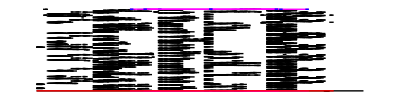

Minimum Contig Length: 2154.

Maximum Contig Length: 2154.

Gaps Between Contigs: {}

Number of Contigs: 1

Lander-Waterman Estimated Average Number of Contigs: 1.76314

Average Contig Length: 2154.

Lander-Waterman Estimated Average Contig Length: 1341.43

Percent of Genome Covered by Contigs: 0.908477

Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: 0.997521

```mathematica
(* Returns list {1, 2, ... , coverage_amount} *)
coverage  = Range[coverageAmount];

(* Standard deviation away from mu *)
sigma = 20.0;

(* Percentage of reads sampled *)
sampleRate=0.6;

(* Include graph theory package *)
<<Combinatorica`

(* This function discards its argument and returns the string representation of the genome you've loaded. I'm not a mathematica adept, so mapping this over a range seemed like a easiest way to implement the 'replicate' function. *)
ReplaceWithGenome[x_] = genome;

copies = Map[ReplaceWithGenome, coverage];
(* POLLUTE walks over a string, changes some characters to account for missense mutations *)
pollute[individualCopy_]:= Module[{copy=individualCopy,chars={},nucleotides="ATCG"},
chars=Characters[copy];
StringJoin[Function[x,Module[{xp=x,r=0,i=0},
i=RandomInteger[{1,4}];
r=RandomReal[];
If[r<errorRate,
xp=StringTake[nucleotides,{i}],
xp]]]/@chars]]

(* polluted list of the coverage copies *)
pollutedCopies = Map[pollute, copies];

(* GenerateNormalNumber 
This is an implementation of the Box-Muller Transform *)
GenerateNormalNumber[m_,s_] := Round[m + s * Sqrt[-2 * Log[Random[]]] * Cos[ 2 * Pi * Random[]]];

(* TAKE LIST generates list of mu +/ sigma, according to genome length *)
takeList[x_] := Module[{a = x, lst={}, r =0},
While[a>0,
r = GenerateNormalNumber[mu,sigma];
If[r<0, r = 0];
If[(a-r) > 0,If[r>15,AppendTo[lst,r]], If[a>15,AppendTo[lst,a]]];
a = a - r;];
lst] 

(* SONICATE returns all fragments with respect to normally distributed lengths *)
sonicate[s_] := Module[{str=s, len = StringLength[s], tl ={}, out={}, f=0},
tl =takeList[len];
While[Length[tl] > 0,
f = First[tl];
tl = Rest[tl];
AppendTo[out,StringTake[str,f]];
str =StringDrop[str,f];
];
out];

(* MAKE POOL returns subset of fragments, according to sampleRate *)
makePool[p_]:= Module[{s=RandomSample[Flatten[Map[sonicate,p]]], r=sampleRate, toTake=0},
toTake=Ceiling[r*Length[s]];
Take[s,toTake]]

(* MAKE SEEDS takes the first 15 bases of each fragment from pool *)
makeSeeds[s_]:=Module[{strLst=s},
Function[x,Module[{xp=x},
StringTake[xp,15]]]/@strLst]

(* POOL: the list of fragments, with respect to sampleRate *)
pool=makePool[pollutedCopies];

(* SEEDS: the first 15 bases of each fragment from pool *)
seeds=makeSeeds[pool];

(* GAPFREESCORE finds the gap free score between a string and a seed. The first character of the string is skipped to prevent the seed from aligning with its origin. *)
gapFreeScore[st_]:=Function[str,Function[seed,Module[{s=str,d=seed, slen=0, dlen=0, out={}, count=1},
slen=StringLength[s];
dlen=StringLength[d];
While[count+dlen < slen,
AppendTo[out,StringTake[str,{count+1,count+dlen}]];
count=count+1;];
Max[Function[x,Module[{xp=x},dlen-EditDistance[xp,d]]]/@out]]]][st]

(* GAPFREEINDEX is a CHEEEEEAT that allows you to find where the fragment is positioned in the original genome *)
gapFreeIndex[st_]:=
Module[{s=st, slen=0, gnm=0, bestScore=0, bestIndex=0, count=1, x},
slen=StringLength[s];
gnm=StringLength[genome];
While[count+slen < gnm,
x=slen-EditDistance[s,StringTake[genome,{count+1,count+slen}]];
If[x>bestScore,
bestIndex=count; bestScore=x;];
count=count+1;];
bestIndex]

(* UNIDENTITYMATRIX makes each [i,i] element 0, each element [i, j] that equals 15 (seed length) = 1 *)
UnIdentityMatrix[in_]:=Module[{n=in,x=1,m},
While[x≤Length[n],
m=n[[x]]; (* m is the xth element of n - the xth seed information element *)
m[[x]]=0; (* set the [i,i] element to 0 *)
n[[x]]=m; (* make changes in actual list *)
x++;];
n]

(* FILTER GRAPH makes numbers 1 if greater than 2 standard deviations above mean of gapFreeScore, else 0 *)
filterGraph[g_]:=Module[{gr=Flatten[g],std,avg},
avg=Mean[gr];
std=2*StandardDeviation[gr];
std=std+avg;
Function[x,Function[y,If[y>std,1,0]]/@x]/@g]

(* DFS is a helper function that is explained later *)
dfs[x_]:=Module[{ii=1, acc={}},
While[ii≤Length[x],
If[x[[ii]] == 0,
 AppendTo[acc,ii];];
ii++;];
acc];

(* EXPLORE is simply a depth first traversal, of graph p starting at vertex x, returns a list of verticies in the order in which they were encountered *)
explore[x_]:=DepthFirstTraversal[p,x]

(* DISPLAY is complicated code that Brendan said not to touch *)
display[ind_,len_]:=Module[{indl=ind,lenl=len, l,x=1,toShow={{Thick,Line[{{1,-1*Sqrt[StringLength[genome]]},{StringLength[genome],-1*Sqrt[StringLength[genome]]}}]}}},
l=Length[indl];
While[x≤l,
AppendTo[toShow,Line[{{indl[[x]],Sqrt[StringLength[genome]]*x/2},{indl[[x]]+lenl[[x]],Sqrt[StringLength[genome]]*x/2}}]];
AppendTo[toShow,{Thick,RGBColor[1,0,0],Line[{{indl[[x]],0},{indl[[x]]+lenl[[x]],0}}]}];
x++;];
toShow]

(* DISPLAY2 is better *)
display2[ind_,len_, indBP_, lenBP_, contigList_]:=Module[{indl=ind,lenl=len, iBP = indBP, lBP = lenBP, l1,l2, l3, y1, y2, x=1, toShow, cList = contigList},
l1=Length[indl];
toShow={{Thick,Line[{{1,-genomeLength/(2*l1)},{genomeLength,-genomeLength/(2*l1)}}]}};
While[x≤l1,
AppendTo[toShow,Line[{{indl[[x]],genomeLength*x/(4*l1)},{indl[[x]]+lenl[[x]],genomeLength*x/(4*l1)}}]];
x++;];
l2 = Length[iBP];
x = 1;
While[x≤l2,
y1 = genomeLength*(l1+x +1)/(4*l1);
y2 = genomeLength*(l1+x)/(4*l1);
AppendTo[toShow,
{{RGBColor[0,1,0], Line[{{iBP[[x]],y1}, {iBP[[x]],y2}}], Line[{{iBP[[x+1]]+25, y1}, {iBP[[x+1]]+25,y2}}]},
{RGBColor[2,0,3], Line[{{iBP[[x]], y1}, {iBP[[x+1]]+25, y1}}]},
{RGBColor[0,0,1], Line[{{iBP[[x]], y2}, {iBP[[x]]+25, y2}}], Line[{{iBP[[x+1]], y2}, {iBP[[x+1]]+25, y2}}]}}];
AppendTo[toShow,{Thick,RGBColor[2,0,3],Line[{{iBP[[x]],-genomeLength/(4*l1)},{iBP[[x+1]]+25,-genomeLength/(4*l1)}}]}];
x=x+2;];
l3 = Length[cList];
x = 1;
While[x≤l3,
AppendTo[toShow,{Thick,RGBColor[1,0,0],Line[{{cList[[x,1]],0},{cList[[x,1]]+cList[[x,2]],0}}]}];
x++];
toShow]

(* ASSEMBLE SEEDS produces a lists of lists, the inner list is a list of gapFreeScores for a particular seed mapped to each string in the pool, the outer list is the list of all these for all seeds *)
assembleSeeds[strlst_,seedlst_]:=Module[{s=strlst,d=seedlst, out={},tmp, c={}},
(* c is a list of functions *)
c=gapFreeScore/@s;
While[Length[d]>0,
tmp=First[d];
d=Rest[d];
(* apply each function c to tmp - gapFreeScore[each seed] mapped to strlst (pool - list of fragments) *)
AppendTo[out,Function[x,Module[{xp=x},xp[tmp]]]/@c]];
out]
(* Start of MATE PAIR code *)

generateMatePairStarts =
Module[{matePairLengths={}, i=1, j = 0},
For[i=1, i<= numMatePairs, i++, 
j = RandomInteger[{1, StringLength[genome]-matePairLength}]; 
AppendTo[matePairLengths, j]]; 
matePairLengths];

matePairStarts = generateMatePairStarts;

(* matePairs is list of pairs of matepair reads (25 bases each) *)
matePairs = Flatten[StringTake[Map[ReplaceWithGenome, {1}], {{#, #+24}, {#+matePairLength - 25, #+matePairLength - 1}}]&/@matePairStarts,1];

findMatePairMatch[pl_, mp_] :=
Module[{pool = pl, matePair = mp, bestHD = 25, curFrag = "", subFrag = "", bestFrag = "", bestSub = "", size = Length[pl], i, j, hd}, 
 For[i = 1, i<size, i++, curFrag = pool[[i]]; 
For[j=1,j<StringLength[curFrag]-25, j++, 
 subFrag = StringTake[curFrag, {j, j+24}];
hd = HammingDistance[subFrag, mp];
If[hd<bestHD, bestFrag = curFrag; bestSub = subFrag; bestHD = hd]]]; bestSub]

findAllMatePairMatches[pl_, mps_] :=
Module[{pool=pl, matePairs = mps, i, j, inner = {}, outer = {}},
For[i=1, i≤numMatePairs, i++,
For[j=1, j≤2, j++, AppendTo[inner, findMatePairMatch[pool, matePairs[[i, j]]]]]; 
AppendTo[outer, inner]; inner={}]; outer]

findOriginalIndex[str_] :=
Module[{string = str, i, gen = Map[ReplaceWithGenome, {1}], length, bestHD = 25, hd, index},
length = StringLength[genome];
For[i = 1, i<= (length-24), i++, hd = HammingDistance[string, First[StringTake[gen, {i, i+24}]]];
If[hd< bestHD, bestHD = hd; index=i]]; index]

joinIndicesAndLengths[ind_, len_] := Module[{i=ind, l=len, x=1, length, new = {}}, 
length = Length[i];
While[x≤length, AppendTo[new, {i[[x]], l[[x]]}];
x++;]; new]

(* find # of contigs *)
findNumContigs[pairedList_] := Module[{pl = pairedList, length, x=2, new},
length = Length[pl];
new = {pl[[1]]};
While[x≤length, If[pl[[x, 1]]>(new[[1, 1]]+new[[1,2]]), 
PrependTo[new, pl[[x]]],
new[[1, 2]] = Max[new[[1,2]], pl[[x,1]]-new[[1, 1]] + pl[[x,2]]]];
x++]; new]

findAvgContigLength[pairedList_] := Module[{pl = pairedList, length, avg = 0, x=1},
length=Length[pl];
While[x≤length, avg = pl[[x, 2]] + avg; 
x++];
avg = (avg / length)]

extractElement[nth_, multiList_] := Module[{n=nth, ml = multiList, length, new={}, x=1},
length = Length[ml];
While[x≤ length, AppendTo[new, ml[[x, n]]];
x++;];
new]

findGapsBetweenContigs[pairedList_] := Module[{pl = Reverse[pairedList], length, x=1, new = {}},
length = Length[pl];
While[x≤ length-1, AppendTo[new, pl[[x+1, 1]] - (pl[[x, 1]]+pl[[x,2]]) ];
x++;];
new]



(* list of list of seed information - each seed information piece is a list of its best gapFreeScore to each fragment *)
g= assembleSeeds[pool,seeds]/.-∞->0;
(* gp is the matrix of 1s and 0s *)
 gp = filterGraph[UnIdentityMatrix[g]];
p=FromAdjacencyMatrix[gp, Type->Directed];
(* toSearch is a list of sums of columns of the matrix gp - each column refers to different fragment *)
(* toSearch also represents the number of incoming edges for each vertex for graph p *)
toSearch=Total/@Transpose[gp];

(* dfs is a list of column numbers whose sum is 0 - the vertex numbers with no incoming edges *)
(* result shows where to start - no incoming edges but potentially outgoing edges if explore returns something *)
(* result is a list of vertices - denoted by their vertex numbers (as many verticies as seeds/fragments) *)
result =Flatten[Select[explore/@dfs[toSearch],Function[x, Length[x]>1]]];
seeds[[result]];

(* this is a CHEAT - tells where to begin *)
indices =gapFreeIndex/@seeds[[result]];

(* lengths is simply a list of string lengths *)
lengths=StringLength/@pool[[result]];

joinedIL = joinIndicesAndLengths[indices, lengths];
joinedIL = Sort[joinedIL,#1[[1]]<#2[[1]]&];

contigList = findNumContigs[joinedIL]

mp = matePairs;
matches = Flatten[findAllMatePairMatches[pool, mp]];
mpIndicies = findOriginalIndex/@matches;

(* For[i=1, i≤ Length[mpIndicies], i=i+2, AppendTo[indices, mpIndicies[[i]]]; AppendTo[lengths,matePairLength]]; *)

Graphics[display2[indices,lengths, mpIndicies, 1000, contigList]]

contigLengths = extractElement[2, contigList];

Print["Minimum Contig Length: ", Min[contigLengths]//N]
Print["Maximum Contig Length: ", Max[contigLengths]//N]
Print["Gaps Between Contigs: ", findGapsBetweenContigs[contigList]]
Print["Number of Contigs: ", Length[contigList]]
numcon = N[((coverageAmount*sampleRate)*genomeLength/mu)*Exp[-(coverageAmount*sampleRate)]];
ansnumcon = If[numcon<1,"<1",numcon];
Print["Lander-Waterman Estimated Average Number of Contigs: ",ansnumcon]
Print["Average Contig Length: ", Mean[contigLengths]//N]
avgcon=N[mu*((Exp[(coverageAmount*sampleRate)]-1)/(coverageAmount*sampleRate))];
Print["Lander-Waterman Estimated Average Contig Length: ",  avgcon]
Print["Percent of Genome Covered by Contigs: ", N[Total[contigLengths]/genomeLength]]
Print["Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: ",  N[1-Exp[-(coverageAmount*sampleRate)]]]
```

```mathematica
(* Read Length = 100, Coverage = 2 *)
```

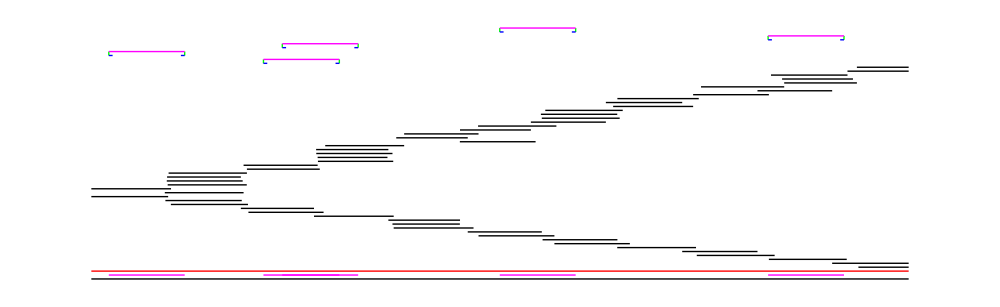
```mathematica
(* Coverage of Phix174 Read Length = 500, Coverage = 8 *)
-Graphics-
"Minimum Contig Length: "5385.
"Maximum Contig Length: "5385.
"Gaps Between Contigs: "{}
"Number of Contigs: "1
"Lander-Waterman Estimated Average Number of Contigs: ""<1"
"Average Contig Length: "5385.
"Lander-Waterman Estimated Average Contig Length: "12553.168491534881
"Percent of Genome Covered by Contigs: "0.999814333457111
"Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: "0.99177025295098
```

-Graphics-

Minimum Contig Length: 5385.

Maximum Contig Length: 5385.

Gaps Between Contigs: {}

Number of Contigs: 1

Lander-Waterman Estimated Average Number of Contigs: <1

Average Contig Length: 5385.

Lander-Waterman Estimated Average Contig Length: 12553.2

Percent of Genome Covered by Contigs: 0.999814

Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: 0.99177

```mathematica
(* Coverage of Phix174 Read Length = 500, Coverage = 6 *)
```

```mathematica
(* Coverage of Phix174 Read Length = 500, Coverage = 4 *)
```

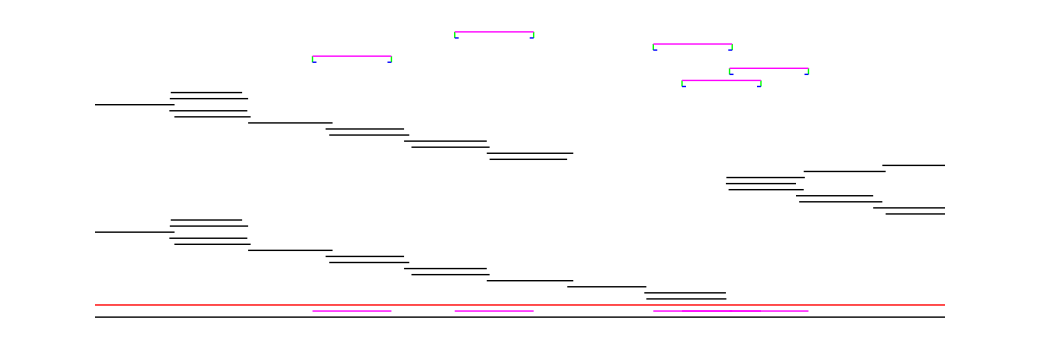
```mathematica
-Graphics-
"Minimum Contig Length: "5385.
"Maximum Contig Length: "5385.
"Gaps Between Contigs: "{}
"Number of Contigs: "1
"Lander-Waterman Estimated Average Number of Contigs: "2.3453131028005236
"Average Contig Length: "5385.
"Lander-Waterman Estimated Average Contig Length: "2088.1617459670006
"Percent of Genome Covered by Contigs: "0.999814333457111
"Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: "0.9092820467105875
```

-Graphics-

Minimum Contig Length: 5385.

Maximum Contig Length: 5385.

Gaps Between Contigs: {}

Number of Contigs: 1

Lander-Waterman Estimated Average Number of Contigs: 2.34531

Average Contig Length: 5385.

Lander-Waterman Estimated Average Contig Length: 2088.16

Percent of Genome Covered by Contigs: 0.999814

Lander-Waterman Estimated Average Percent of Genome Covered by Contigs: 0.909282